```mathematica
Needs["NDSolve`FEM`"];
```

```mathematica
ClearAll[ eqn, sol,kappa,ymax,ydat,T0,L,Ltri,x,y,z,z0,Xc,Yc,Rc,Rh,Rw,phiMin, phiMax,phiMinDeg, phiMaxDeg, rad2deg, powerDensity3D, powerDensityInDegrees3D, cpsInterFunc,copperCylinderRegion,copperCylinderEdge, copperCylinderEdgeMesh, missingArcRegion,missingArcRegionBoundaryMesh, missingBeamCylinder,missingBeamCylinderEdge, missingBeamCylinderBoundaryMesh, missingRegion, missingRegionBoundaryMesh, meshRegion];
```

```mathematica
cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/CPS_Temperature_With_Mathematica/klcps_31b_swapped.m"]
```

InterpolatingFunction[{{0.0125, 5.9875}, {-5.21417, 1.02538}, {0.25, 93.75}}, <>]

```mathematica
kappa=0.00385;T0=100.0;
ydat=6.0;ymax=10.0;
L=94.0;z0=L/2.; 
Ltri=54.0;Rh=0.5;
Xc=0.0;Yc=2.0;Rc=8.0; 
Rw=3.758770483; 
phiMin=-29/18*π; phiMax=7/18*π; 
rad2deg=(90./ArcCos[0]); phiMinDeg = phiMin * rad2deg; phiMaxDeg = phiMax * rad2deg;
```

```mathematica
(*powerDensity3D[x_,y_,z_]= cpsInterFunc[y ,x,z]/1000.;*)
```

```mathematica
powerDensity3D[x_,y_,z_]=Piecewise[{{ cpsInterFunc[y ,x,z]/1000.,-5.21417<=x<=1.02538333333&&0.0125<=y<=5.9875&&0.25<=z<=93.75}},0.000];
```

```mathematica
powerDensityInDegrees3D[x_,y_,z_]:= powerDensity3D[(x/(57.2957795131)),y,z];
```

```mathematica
(*NIntegrate[y*powerDensity3D[x,y,z],{x,-5*Pi/3,Pi/3},{y,0,ymax},{z,0,L},WorkingPrecision->9]*)
```

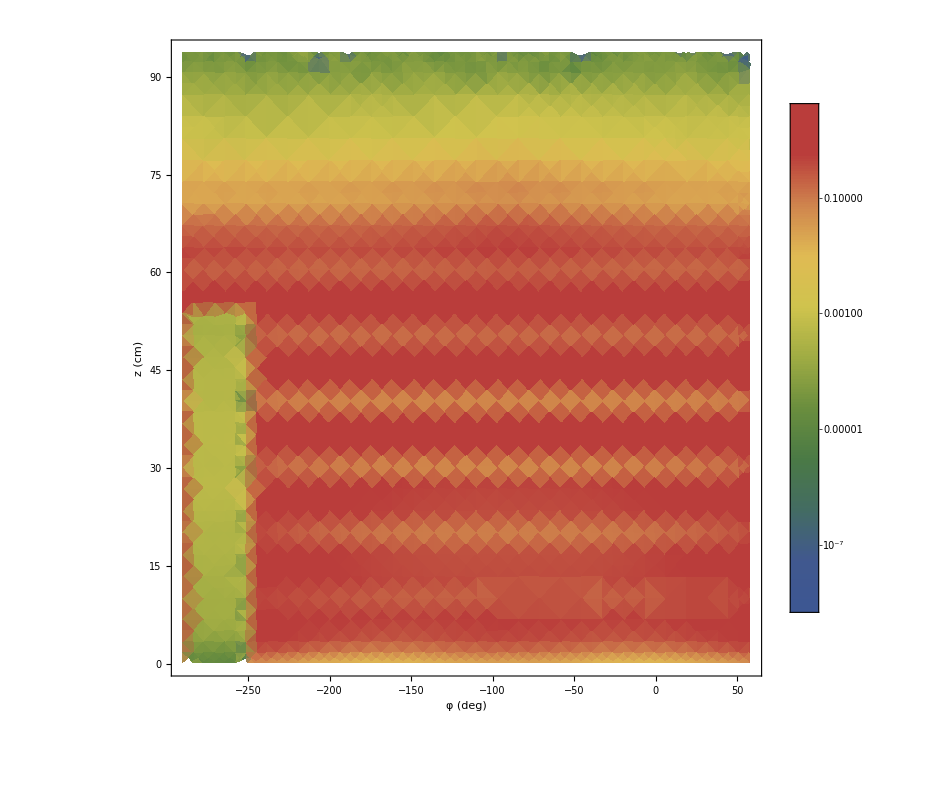

```mathematica
DensityPlot[powerDensityInDegrees3D[x,0.2,z],{x,phiMinDeg,phiMaxDeg},{z,0,L},ColorFunction->{"DarkRainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"φ (deg)", "z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

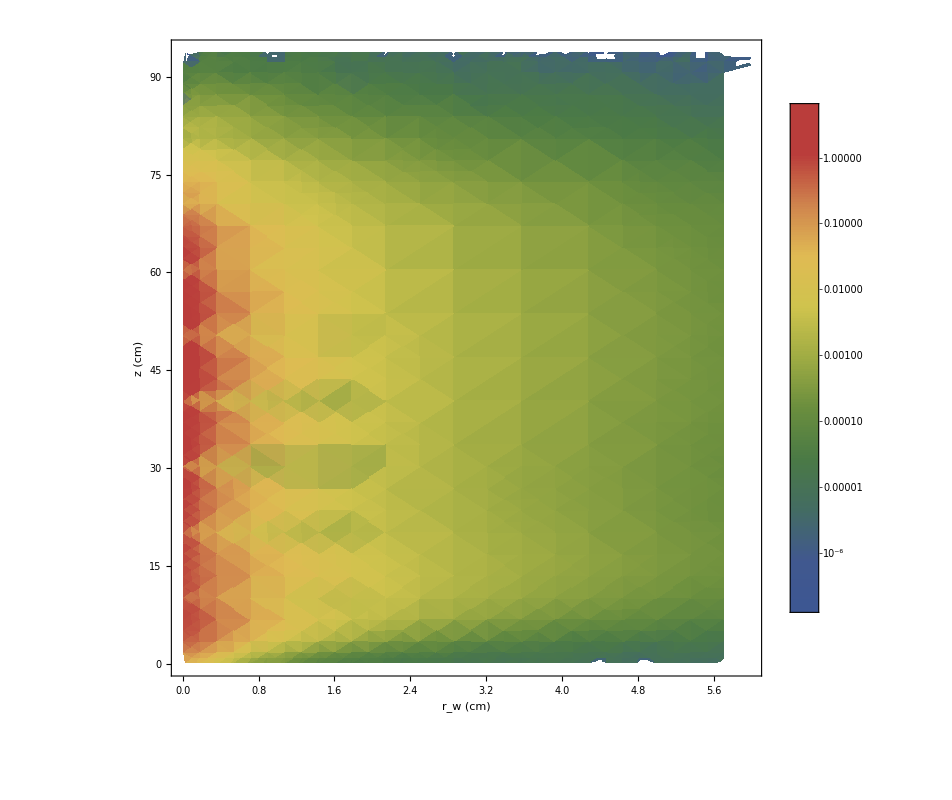

```mathematica
DensityPlot[powerDensityInDegrees3D[-120.,y,z],{y,0.0,ymax},{z,0,L},ColorFunction->{"DarkRainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"r_w (cm)", "z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

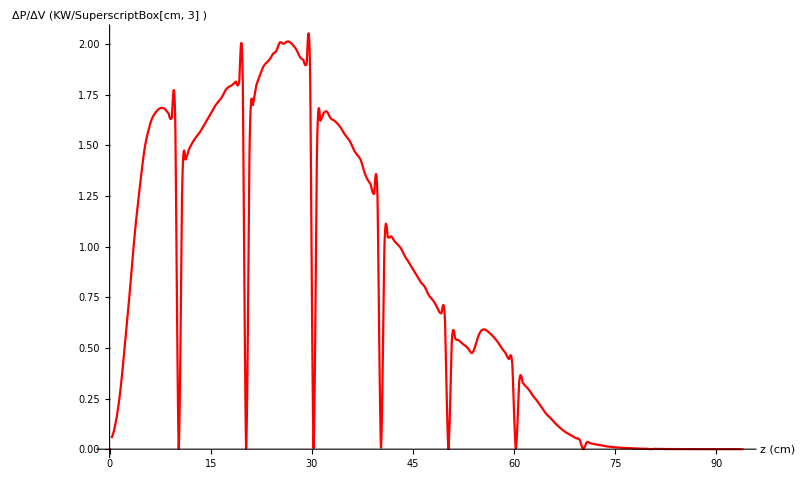

```mathematica
Plot[powerDensityInDegrees3D[-240.0,0.3,z],{z,0,L}, AxesLabel->{"z (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

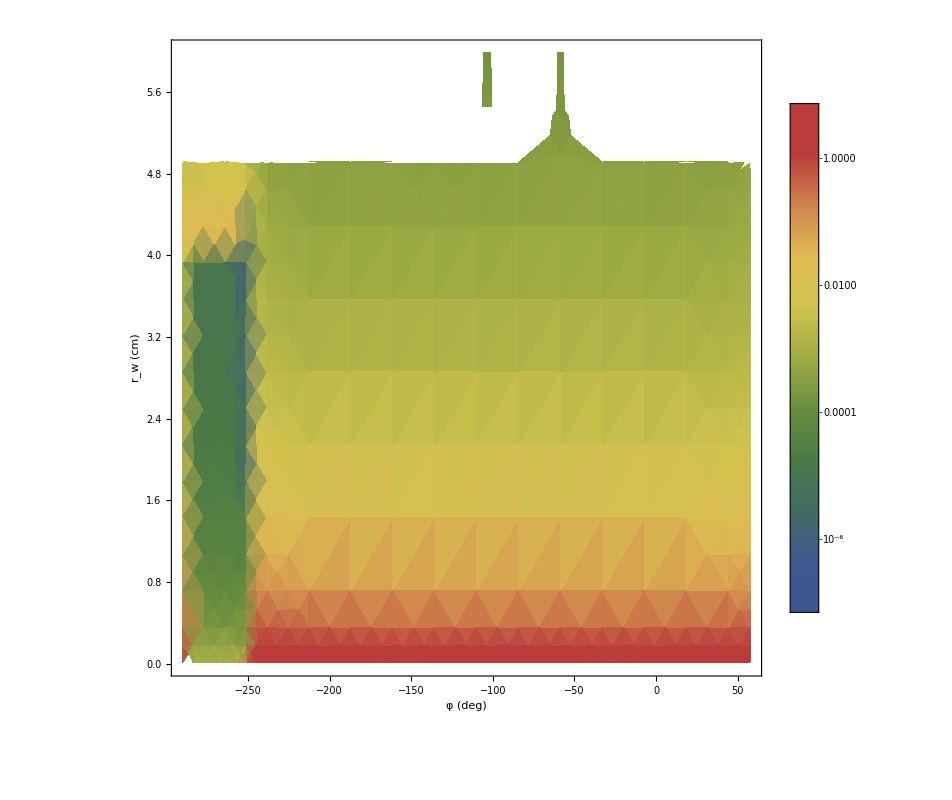

```mathematica
DensityPlot[powerDensityInDegrees3D[x,y,45],{x,phiMinDeg,phiMaxDeg},{y,0.0,ymax},ColorFunction->"DarkRainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"φ (deg)", "r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
N[powerDensity3D[-50/rad2deg,5.7,55]]
```

0.000182168

```mathematica
N[phiMax]
```

1.22173

```mathematica
1.0471975511965976
```

1.0472

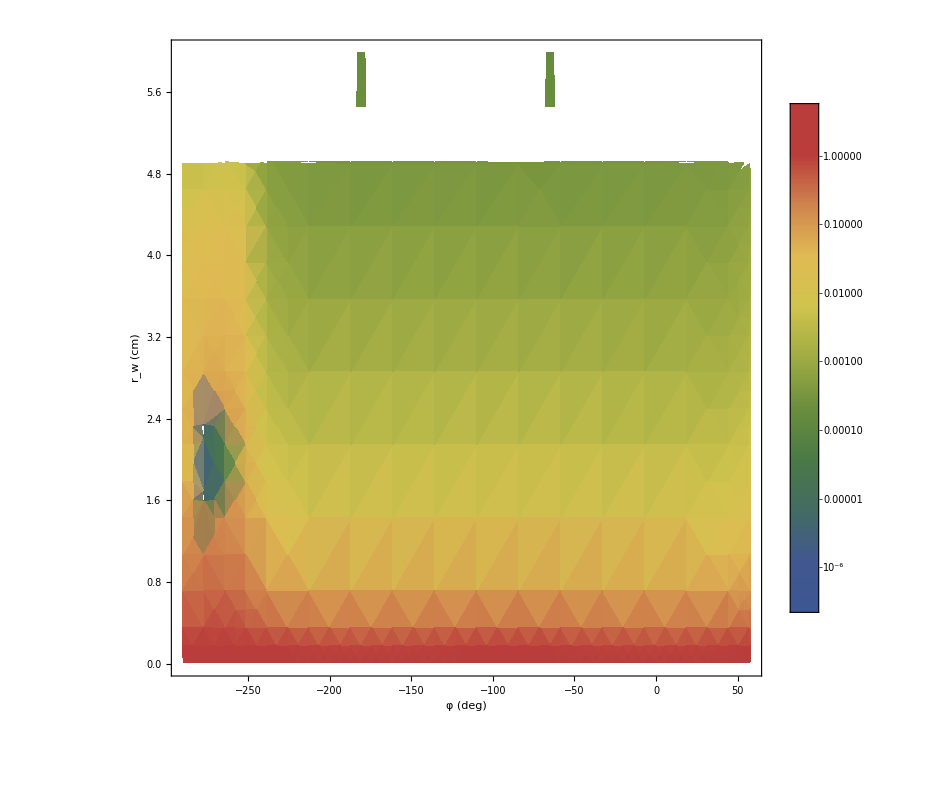

```mathematica
DensityPlot[powerDensityInDegrees3D[x,y,55],{x,phiMinDeg,phiMaxDeg},{y,0.0,ymax},ColorFunction->"DarkRainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"φ (deg)", "r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
powerDensity3D[-50/rad2deg,5.6, z0]
```

0.000206331

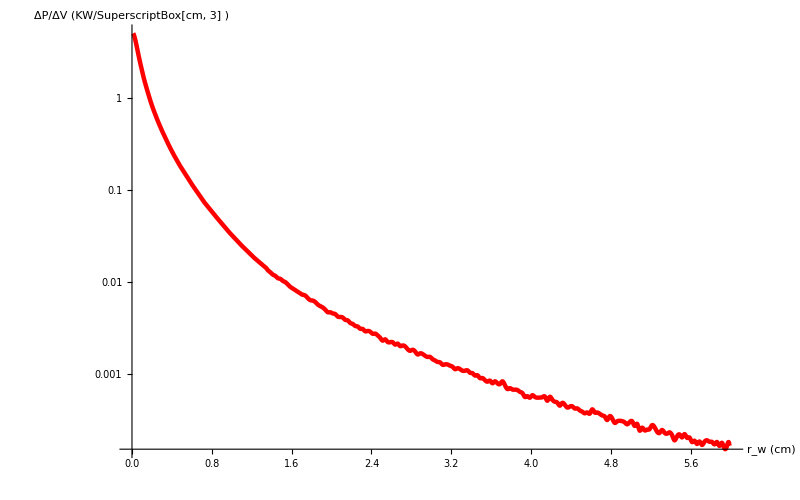

```mathematica
LogPlot[powerDensityInDegrees3D[-60.,y,55],{y,0,ydat},AxesLabel->{"r_w (cm)", "ΔP/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
copperCylinderRegion=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)<=Rc^2,{{x,phiMin,phiMax},{y,0,ymax},{z,0,L}}];
```

```mathematica
(*RegionPlot3D[copperCylinderRegion, Mesh->None]*)
```

```mathematica
(*copperCylinderEdge=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)==Rc^2,{{x,phiMin,phiMax},{y,0,ymax},{z,0,L}}];*)
```

```mathematica
(*copperCylinderEdgeMesh = ToBoundaryMesh[copperCylinderEdge, MeshQualityGoal->"Maximal", BoundaryMeshGenerator->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.01}];*)
(*copperCylinderEdgeMesh["Wireframe"]*)
```

```mathematica
missingArcRegion=ImplicitRegion[y≤(Rw*Sin[-29/18*π]/Sin[x]),{{x,-29/18*π,-25/18*π},{y,0,Rw},{z,0,Ltri}}];
(*RegionPlot3D[missingArcRegion]*)
```

```mathematica
(*missingArcRegionBoundaryMesh = ToBoundaryMesh[missingArcRegion, MeshQualityGoal->"Maximal", BoundaryMeshGenerator->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.01}];*)(*missingArcRegionBoundaryMesh["Wireframe"]*)
```

```mathematica
missingBeamCylinder=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)<=Rh^2,{{x,phiMin,phiMax},{y,0,ymax},{z,Ltri,L}}];
```

```mathematica
(*missingBeamCylinderEdge=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)==Rh^2,{{x,phiMin,phiMax},{y,0,ymax},{z,Ltri,L}}];*)
```

```mathematica
(*missingBeamCylinderBoundaryMesh=ToBoundaryMesh[missingBeamCylinderEdge, MeshQualityGoal->"Maximal", BoundaryMeshGenerator->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.01}];*)
(*missingBeamCylinderBoundaryMesh["Wireframe"]*)
```

```mathematica
missingRegion = RegionUnion[missingArcRegion,missingBeamCylinder];
```

```mathematica
copperRegion = RegionDifference[copperCylinderRegion,RegionUnion[missingArcRegion,missingBeamCylinder]];
```

```mathematica
(*RegionPlot3D[copperRegion]*)
```

```mathematica
(*missingRegionBoundaryMesh = ToBoundaryMesh[missingRegion, MeshQualityGoal->"Maximal", BoundaryMeshGenerator->"Continuation", MaxBoundaryCellMeasure->{"Length"->0.01}];*)
(*missingRegionBoundaryMesh["Wireframe"]*)
```

```mathematica
(*meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal", BoundaryMeshGenerator->"Continuation",MaxBoundaryCellMeasure->{"Length"->0.01}, MaxCellMeasure->{"Length"->0.2}];*)
meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal",MaxBoundaryCellMeasure->{"Length"->0.05},MaxCellMeasure->{"Length"->0.3}];
(*RegionPlot3D[copperRegion, Mesh->All]*)
```

```mathematica
(*missingRegionBoundaryMesh = ToBoundaryMesh[missingRegion, MeshQualityGoal->"Maximal"];*)
```

```mathematica
(*meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal"];*)
```

```mathematica
(*meshRegion["Wireframe"]*)
```

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z},"Cylindrical"]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,{x,y,z}∈missingArcRegionBoundaryMesh] + NeumannValue[0.0,{x,y,z}∈missingBeamCylinderBoundaryMesh];*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{y,x,z},"Cylindrical"]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,{x,y,z}∈RegionBoundary@missingArcRegion] + NeumannValue[0.0,{x,y,z}∈RegionBoundary@missingBeamCylinder] ;
```

```mathematica
(*sol=NDSolveValue[{eqn,DirichletCondition[u[x,y,z]==T0,((y*Sin[x]-Yc)^2+(y*Cos[x])^2==Rc^2)]}, u,{x, y,z} ∈ meshRegion ];*)
```

```mathematica
sol=NDSolveValue[{eqn,DirichletCondition[u[x,y,z]==T0,((y*Sin[x]-Yc)^2+(y*Cos[x])^2==Rc^2)]}, u,{x, y,z} ∈   meshRegion ];
```

ImplicitRegion::ivar: -4.41147 is not a valid variable.

RegionBoundary::reg: ImplicitRegion[9.88814≤3.53209 Csc[-4.41147]&&-(29 π)/18≤-4.41147≤-(25 π)/18&&0≤9.88814≤3.75877&&0≤94.≤54.,{-4.41147,9.88814,94.}] is not a correctly specified region.

ImplicitRegion::ivar: -4.62813 is not a valid variable.

RegionBoundary::reg: ImplicitRegion[9.99113≤3.53209 Csc[-4.62813]&&-(29 π)/18≤-4.62813≤-(25 π)/18&&0≤9.99113≤3.75877&&0≤94.≤54.,{-4.62813,9.99113,94.}] is not a correctly specified region.

ImplicitRegion::ivar: -4.41147 is not a valid variable.

General::stop: Further output of ImplicitRegion::ivar will be suppressed during this calculation.

RegionBoundary::reg: ImplicitRegion[9.78723≤3.53209 Csc[-4.41147]&&-(29 π)/18≤-4.41147≤-(25 π)/18&&0≤9.78723≤3.75877&&0≤94.≤54.,{-4.41147,9.78723,94.}] is not a correctly specified region.

General::stop: Further output of RegionBoundary::reg will be suppressed during this calculation.

CompiledFunction::cfta: Argument {Boole[{-4.41147,9.88814,94.}∈RegionBoundary[ImplicitRegion[9.88814≤Times[«2»]&&Times[«2»]≤-4.41147≤Times[«2»]&&0≤9.88814≤3.75877&&0≤94.≤54.,{-4.41147,9.88814,94.}]]],Boole[{-4.62813,9.99113,94.}∈RegionBoundary[ImplicitRegion[9.99113≤Times[«2»]&&Times[«2»]≤-4.62813≤Times[«2»]&&0≤9.99113≤3.75877&&0≤94.≤54.,{-4.62813,9.99113,94.}]]],«47»,Boole[{-4.62813,9.99113,89.1196}∈RegionBoundary[ImplicitRegion[9.99113≤Times[«2»]&&Times[«2»]≤-4.62813≤Times[«2»]&&0≤9.99113≤3.75877&&0≤89.1196≤54.,{-4.62813,9.99113,89.1196}]]],«95107»} at position 1 should be a rank 1 tensor of machine-size integers.

CompiledFunction::cfta: Argument {Boole[{-4.41147,9.88814,94.}∈RegionBoundary[ImplicitRegion[Plus[«2»]≤0.25&&Times[«2»]≤-4.41147≤Times[«2»]&&0≤9.88814≤10.&&54.≤94.≤94.,{-4.41147,9.88814,94.}]]],Boole[{-4.62813,9.99113,94.}∈RegionBoundary[ImplicitRegion[Plus[«2»]≤0.25&&Times[«2»]≤-4.62813≤Times[«2»]&&0≤9.99113≤10.&&54.≤94.≤94.,{-4.62813,9.99113,94.}]]],«47»,Boole[{-4.62813,9.99113,89.1196}∈RegionBoundary[ImplicitRegion[Plus[«2»]≤0.25&&Times[«2»]≤-4.62813≤Times[«2»]&&0≤9.99113≤10.&&54.≤89.1196≤94.,{-4.62813,9.99113,89.1196}]]],«95107»} at position 1 should be a rank 1 tensor of machine-size integers.

```mathematica
(*sol=NDSolveValue[{eqn,PeriodicBoundaryCondition[u[x,y,z], x==-Pi, TranslationTransform[{2*Pi,0,0}] ], DirichletCondition[u[x,y,z]==T0,((y*Sin[x]-Yc)^2+(y*Cos[x])^2==Rc^2)]}, u,{x, y,z} ∈ meshRegion]*)
```

```mathematica
(*Export["/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_cps55_p3meshFromp05bmesh_nvFrom2RBs_dcFromFormula.m", sol]*)
```

/home/hovanes/Documents/Wolfram Mathematica/CPS_Temperature_With_Mathematica/t_distribution_3D_cps55_p3meshFromp05bmesh_nvFrom2RBs_dcFromFormula.m

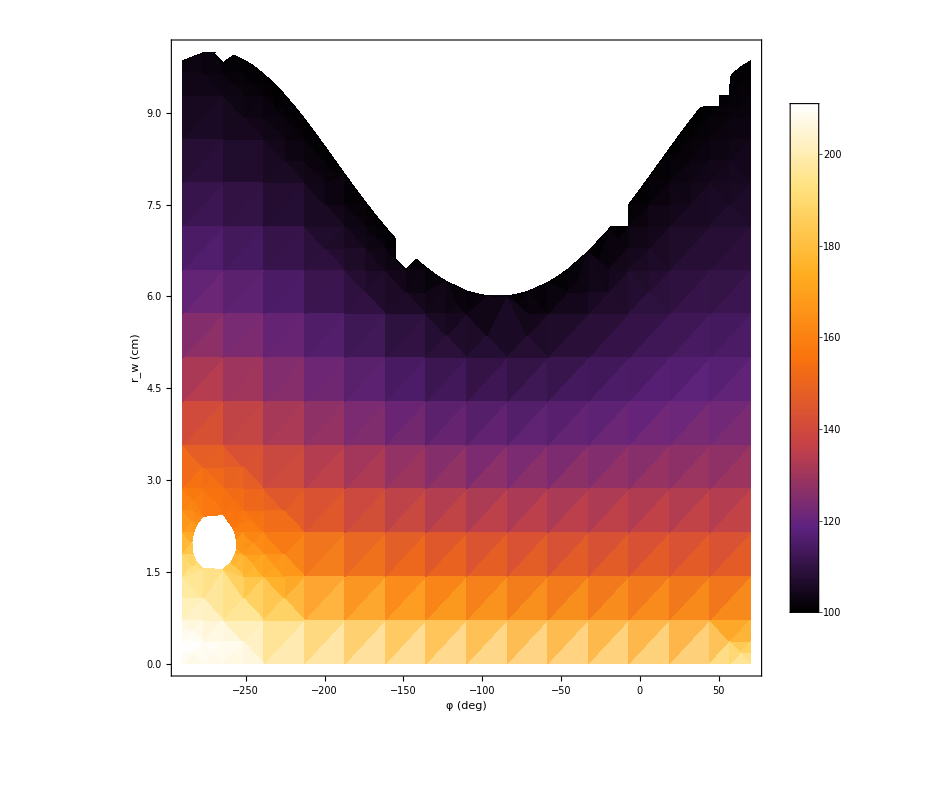

```mathematica
DensityPlot[sol[x/rad2deg,y,55], {x,phiMin*rad2deg,phiMax*rad2deg},{y,0,ymax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,240},ImageSize->{800,800},FrameLabel->{"φ (deg)", "r_w (cm)", "T (^oC)"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

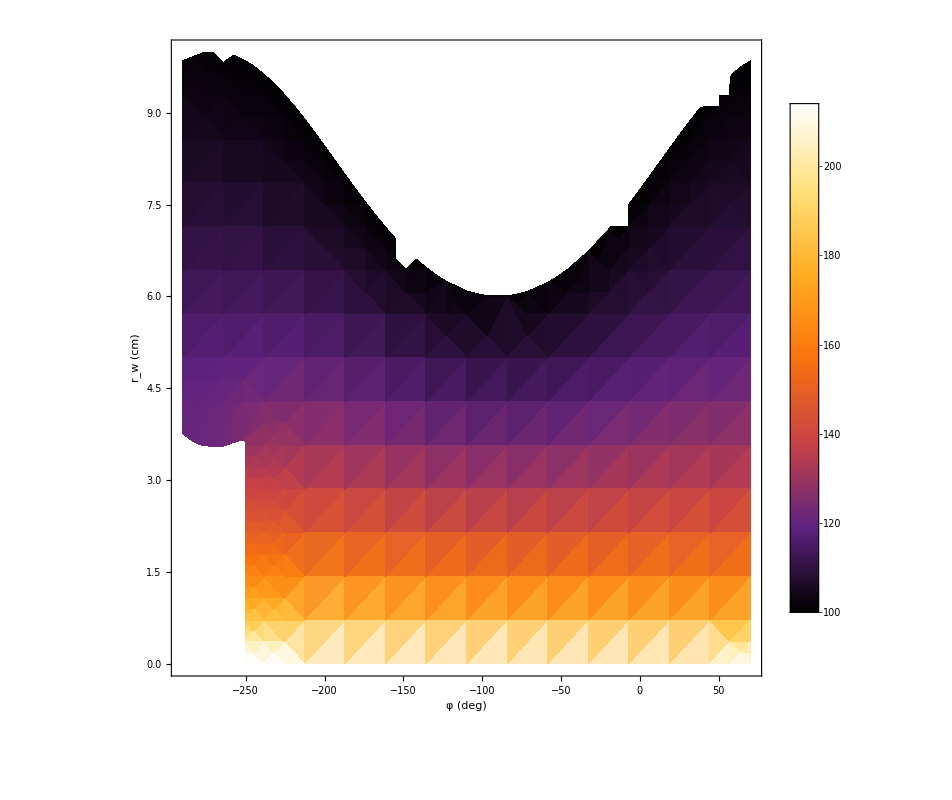

```mathematica
DensityPlot[sol[x/rad2deg,y,45], {x,phiMin*rad2deg,phiMax*rad2deg},{y,0,ymax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,240},ImageSize->{800,800},FrameLabel->{"φ (deg)", "r_w (cm)", "T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

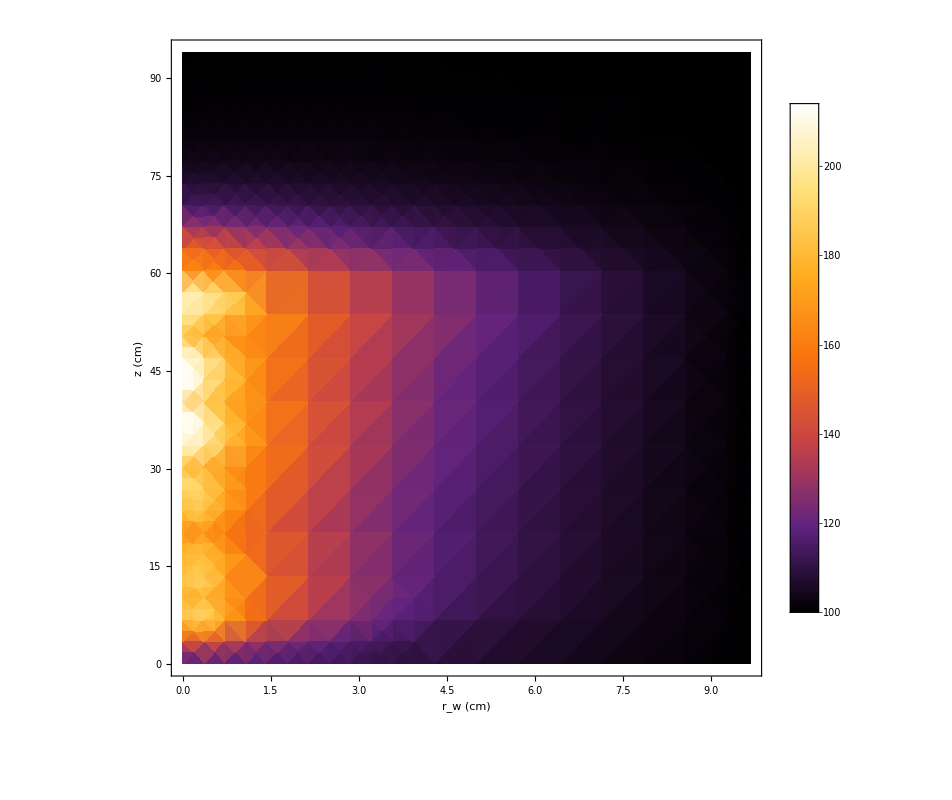

```mathematica
DensityPlot[sol[-240/rad2deg,y,z], {y,0,ymax},{z,0,L},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,240},ImageSize->{800,800},FrameLabel->{ "r_w (cm)", "z (cm)","T (^oC)"} , LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->1]
```

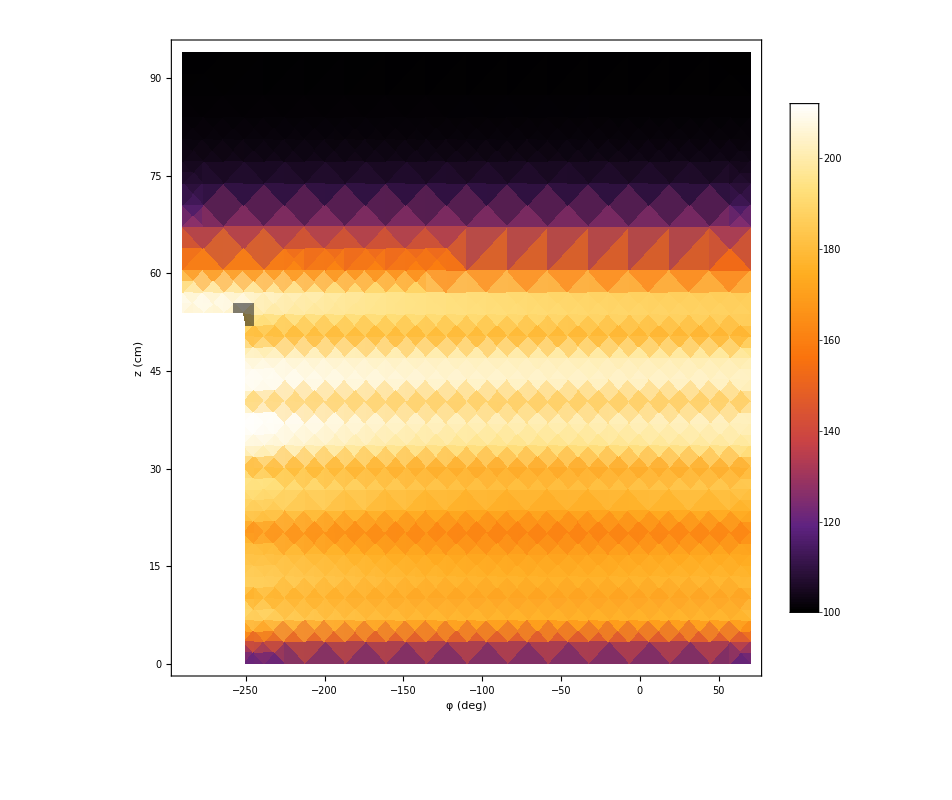

```mathematica
DensityPlot[sol[x/rad2deg,0.2,z],{x,phiMin*rad2deg, phiMax*rad2deg} ,{z,0,L},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,240},ImageSize->{800,800},FrameLabel->{ "φ (deg)", "z (cm)","T (^oC)"} , LabelStyle->{22,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
SliceContourPlot3D[sol[x/rad2deg,y,z], "CenterPlanes",{x,phiMin*rad2deg, phiMax*rad2deg},{y,0,ymax},{z,0,L}, PlotTheme->"Detailed",PlotRange->Full,  ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "φ (deg)", "r_w (cm)","z (cm)"},LabelStyle->{22GrayLevel[0],Italic}]
```

-Graphics3D-

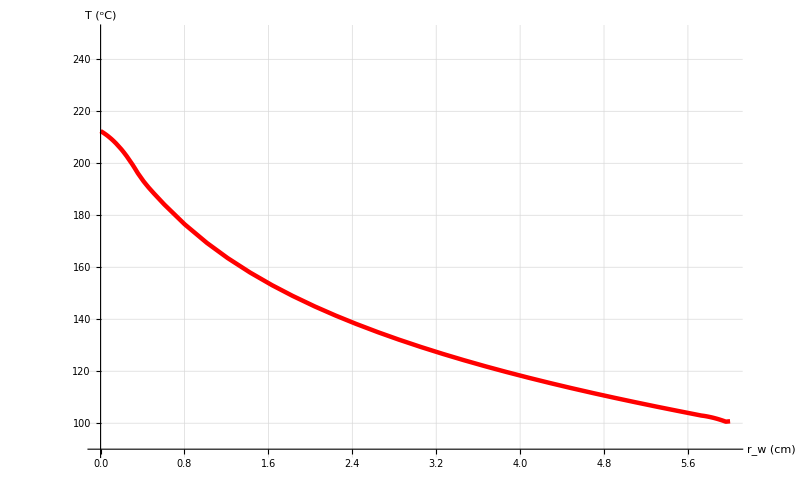

```mathematica
Plot[sol[-90/rad2deg,y,45], {y,0.0,ymax},GridLines->Automatic,PlotRange->{T0-10,250},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

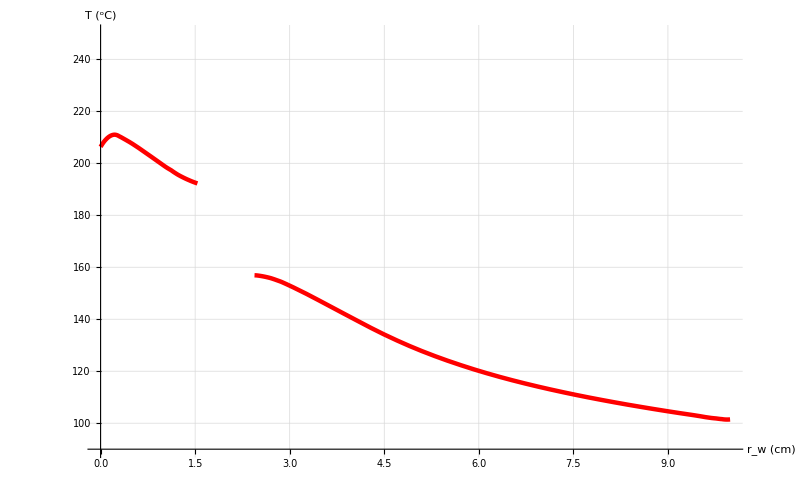

```mathematica
Plot[sol[-270/rad2deg,y,55], {y,0.0,ymax},GridLines->Automatic,PlotRange->{T0-10,250},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

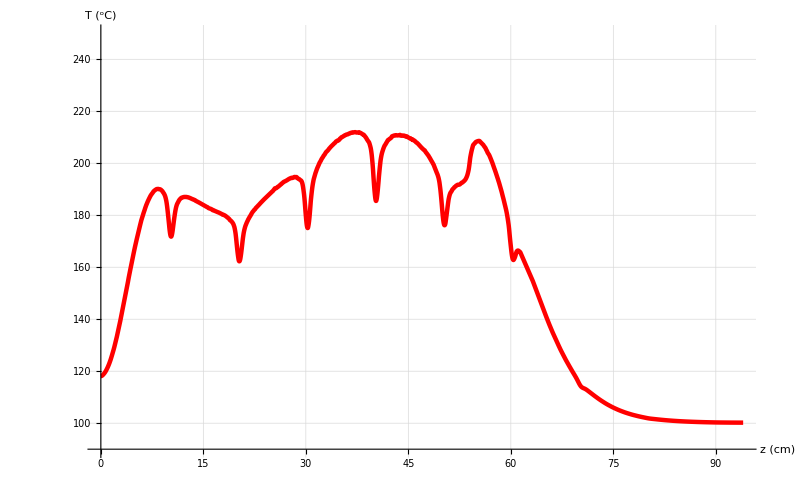

```mathematica
Plot[sol[-240/rad2deg,0.2,z], {z,0.0,L},GridLines->Automatic,PlotRange->{T0-10,250},AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

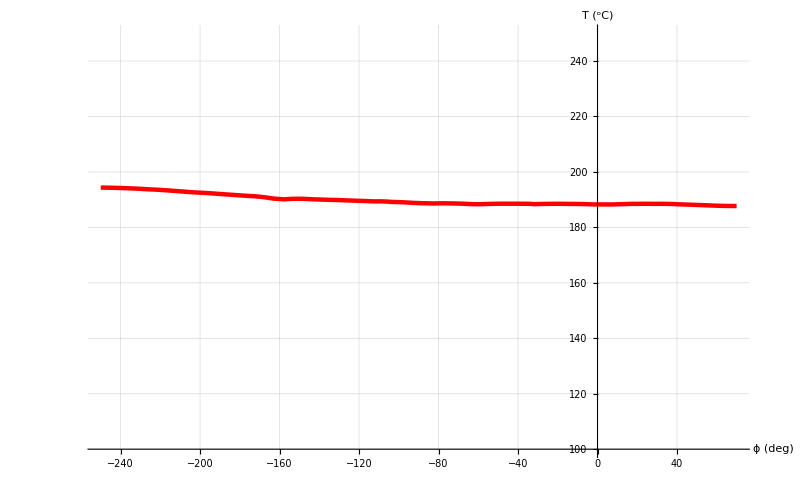

```mathematica
Plot[sol[x/rad2deg,0.5,45], {x,phiMin*rad2deg, phiMax*rad2deg},GridLines->Automatic,PlotRange->{T0,250},AxesLabel->{"ϕ (deg)", "T (^oC)"} ,LabelStyle-> {22,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```